## Numerical Example (Non-homog. b.c. for u and Homog. for p):

```mathematica
lambda=1;
mu=1;
alpha=0;
c0=0;
K=IdentityMatrix[2];
```

```mathematica
Clear[lambda,mu,alpha,c0]
```

### Displacement :

```mathematica
u[x_,y_,t_]:={x^2,y^2}
```

Dirichlet boundary conditions : (they are not homogeneous)

```mathematica
u[0,y,t]
```

{0,y^2}

```mathematica
u[1,y,t]
```

{1,y^2}

```mathematica
u[x,0,t]
```

{x^2,0}

```mathematica
u[x,1,t]
```

{x^2,1}

ContourPlot of the Magnitude of the displacement (Euclidean norm) :

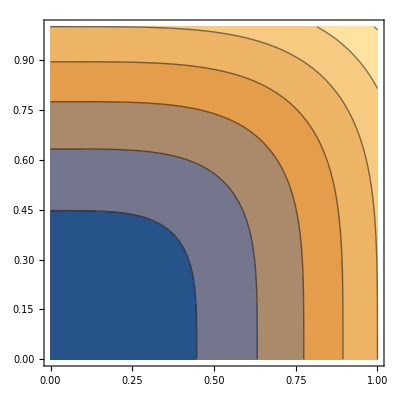

```mathematica
ContourPlot[Sqrt[(x^2)^2+(y^2)^2]/.t->0.001,{x,0,1},{y,0,1}]
```

### Pressure:

```mathematica
p[x_,y_,t_]:= 0
```

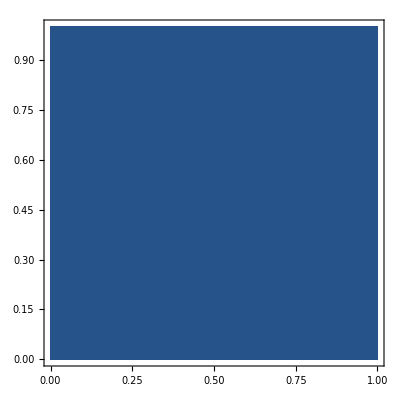

```mathematica
ContourPlot[p[x,y,t],{x,0,1},{y,0,1}]
```

### Elastic Stress:

```mathematica
Gradu[x_,y_,t_]:={{D[u[x,y,t][[1]], x],D[u[x,y,t][[1]], y]},{D[u[x,y,t][[2]], x],D[u[x,y,t][[2]], y]}}
```

```mathematica
Gradu[x,y,t]
```

{{2 x,0},{0,2 y}}

Let us define ϵ (u) :

```mathematica
w=1/2*(Gradu[x,y,t]+Transpose[Gradu[x,y,t]])//Simplify
```

{{2 x,0},{0,2 y}}

Let us compute the stress σ= A^-1 ϵ(u): (Using the expression for A^-1 given in equation (3 . 2 . 9) of Ambartsumyan PhD. Thesis)

```mathematica
Sigmae[x_,y_,t_]:=2mu w+lambda Tr[w]IdentityMatrix[2]//Simplify
```

```mathematica
Sigmae[x,y,t]
```

{{4 mu x+2 lambda (x+y),0},{0,4 mu y+2 lambda (x+y)}}

Let us define the stress function as the previous expression :

### Stress:

```mathematica
Sigma[x_,y_,t_]:=Sigmae[x,y,t]-alpha {{p[x,y,t],0},{0,p[x,y,t]}}//Simplify
```

```mathematica
Sigma[x,y,t]
```

{{4 mu x+2 lambda (x+y),0},{0,4 mu y+2 lambda (x+y)}}

ContourPlot of the Magnitude of the first row of σ :

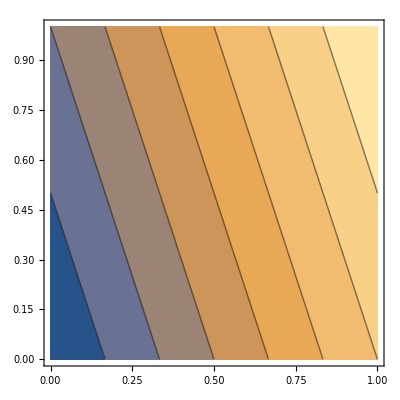

```mathematica
ContourPlot[Sqrt[(4 mu x+2 lambda (x+y))^2+(0)^2]/.{lambda->1,mu->1,alpha->1},{x,0,1},{y,0,1}]
```

ContourPlot of the Magnitude of the second row of σ :

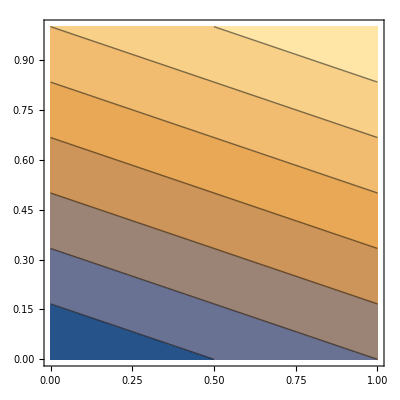

```mathematica
ContourPlot[Sqrt[(0)^2+(4 mu y+2 lambda (x+y))^2]/.{lambda->1,mu->1,alpha->1},{x,0,1},{y,0,1}]
```

### Rotation :

```mathematica
1/2*(Gradu[x,y,t]-Transpose[Gradu[x,y,t]])//Simplify
```

{{0,0},{0,0}}

ContourPlot of the element in the first row and second column of the rotation:

```mathematica
ContourPlot[0,{x,0,1},{y,0,1}]
```

-Graphics-

### Darcy velocity :

```mathematica
K = perm*IdentityMatrix[2];
```

```mathematica
-K.{D[p[x,y,t],x],D[p[x,y,t],y]}//Simplify
```

{0,0}

```mathematica
z[x_,y_,t_]:={0,0}
```

```mathematica
ContourPlot[Sqrt[(0)^2+(0)^2]/.perm->1,{x,0,1},{y,0,1}]
```

-Graphics-

### Source term f :

```mathematica
Sigma[x,y,t]
```

{{4 mu x+2 lambda (x+y),0},{0,4 mu y+2 lambda (x+y)}}

```mathematica
f[x_,y_,t_]:={-Div[{Sigma[x,y,t][[1,1]],Sigma[x,y,t][[1,2]]},{x,y}],-Div[{Sigma[x,y,t][[2,1]],Sigma[x,y,t][[2,2]]},{x,y}]}
```

```mathematica
f[x,y,t]//Simplify
```

{-2 (lambda+2 mu),-2 (lambda+2 mu)}

### Source term q :

```mathematica
u[x,y,t]
```

{x^2,y^2}

```mathematica
z[x,y,t]
```

{0,0}

```mathematica
D[c0 p[x,y,t]+alpha (D[u[x,y,t][[1]],x]+D[u[x,y,t][[2]],y]),t]+D[z[x,y,t][[1]],x]+D[z[x,y,t][[2]],y]//Simplify
```

0

```mathematica
q[x_,y_,t_]:=0
```